```mathematica
ClearAll["Global`*"]
```

```mathematica
starvation =  ts*-Bm/(Em*Log[1-f0*M^(γ-1)])
recovery = ts*- ((η-1)*Bm/Em)/(Log[1-(M*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])
```

-(Bm ts)/(Em Log[1-f0 M^(-1+γ)])

-(Bm ts (-1+η))/(Em (Log[1-((B0/Bm)^(1/(-1+η)) M)^(1-η)]-Log[1-((B0/Bm)^(1/(-1+η)) M (1-f0 M^(-1+γ)))^(1-η)]))

```mathematica
starvation
```

-(Bm ts)/(Em Log[1-f0 M^(-1+γ)])

```mathematica
recovery
```

-(Bm ts (-1+η))/(Em (Log[1-((B0/Bm)^(1/(-1+η)) M)^(1-η)]-Log[1-((B0/Bm)^(1/(-1+η)) M (1-f0 M^(-1+γ)))^(1-η)]))

```mathematica
Ratio = FullSimplify[starvation/recovery]
```

(Log[1-((B0/Bm)^(1/(-1+η)) M)^(1-η)]-Log[1-((B0/Bm)^(1/(-1+η)) (M-f0 M^γ))^(1-η)])/((-1+η) Log[1-f0 M^(-1+γ)])

```mathematica
RatioAnalytic = Ratio/.{
η->3/4,
γ->1.19,
f0->0.0202,
B0->1.9*10^(-2),
Bm->0.0245
}
```

-(4 (Log[1-1.28947 M^(1/4)]-Log[1-1.28947 (M-0.0202 M^1.19)^(1/4)]))/Log[1-0.0202 M^0.19]

```mathematica
RatioAnalytic/.{M->0.36784590002898243}
```

6049.36+0. ⅈ

```mathematica
FullSimplify[D[(Log[1-((B0/Bm)^(1/(-1+η)) M)^(1-η)]-Log[1-((B0/Bm)^(1/(-1+η)) (M-f0 M^γ))^(1-η)])/((-1+η) Log[1-f0 M^(-1+γ)]),M]]
```

1/(Log[1-f0 M^(-1+γ)]^2)((1/(-M+(B0/Bm)^(1/(1-η)) ((B0/Bm)^(1/(-1+η)) M)^η)+(M-f0 M^γ γ)/(M (M-f0 M^γ-(B0/Bm)^(1/(1-η)) ((B0/Bm)^(1/(-1+η)) (M-f0 M^γ))^η))) Log[1-f0 M^(-1+γ)]-(f0 M^(-1+γ) (-1+γ) (Log[1-((B0/Bm)^(1/(-1+η)) M)^(1-η)]-Log[1-((B0/Bm)^(1/(-1+η)) (M-f0 M^γ))^(1-η)]))/((-M+f0 M^γ) (-1+η)))

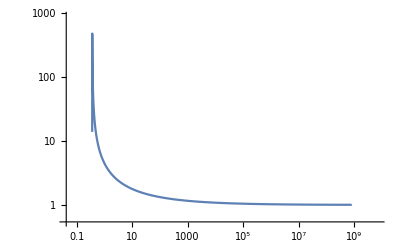

```mathematica
LogLogPlot[Re[RatioAnalytic],{M,0.01,10^20},PlotRange->All]
```

```mathematica
FindMaximum[Re[RatioAnalytic],M]
FindMinimum[Re[RatioAnalytic],M]
```

FindMaximum::sdprec: Line search unable to find a sufficient increase in the function value with MachinePrecision digit precision.

{6049.36,{M→0.367846}}

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

{1.00715,{M→4.92266×10^8}}

```mathematica
Re[RatioAnalytic]/.M->10^10
```

-6.79748

```mathematica
DRatioAnalytic = D[RatioAnalytic,M]
DDRatioAnalyic = D[DRatioAnalytic,M]
```

-(4 (-0.322368/((1-1.28947 M^(1/4)) M^(3/4))+(0.322368 (1-0.024038 M^0.19))/((M-0.0202 M^1.19)^(3/4) (1-1.28947 (M-0.0202 M^1.19)^(1/4)))))/Log[1-0.0202 M^0.19]-(0.015352 (Log[1-1.28947 M^(1/4)]-Log[1-1.28947 (M-0.0202 M^1.19)^(1/4)]))/((1-0.0202 M^0.19) M^0.81 Log[1-0.0202 M^0.19]^2)

-(0.030704 (-0.322368/((1-1.28947 M^(1/4)) M^(3/4))+(0.322368 (1-0.024038 M^0.19))/((M-0.0202 M^1.19)^(3/4) (1-1.28947 (M-0.0202 M^1.19)^(1/4)))))/((1-0.0202 M^0.19) M^0.81 Log[1-0.0202 M^0.19]^2)-1/Log[1-0.0202 M^0.19]4 (0.241776/((1-1.28947 M^(1/4)) M^(7/4))-0.103921/((1-1.28947 M^(1/4))^2 M^(3/2))+(0.103921 (1-0.024038 M^0.19)^2)/((M-0.0202 M^1.19)^(3/2) (1-1.28947 (M-0.0202 M^1.19)^(1/4))^2)-(0.241776 (1-0.024038 M^0.19)^2)/((M-0.0202 M^1.19)^(7/4) (1-1.28947 (M-0.0202 M^1.19)^(1/4)))-0.00147233/(M^0.81 (M-0.0202 M^1.19)^(3/4) (1-1.28947 (M-0.0202 M^1.19)^(1/4))))-(0.000117842 (Log[1-1.28947 M^(1/4)]-Log[1-1.28947 (M-0.0202 M^1.19)^(1/4)]))/((1-0.0202 M^0.19)^2 M^1.62 Log[1-0.0202 M^0.19]^3)+(0.0124351 (Log[1-1.28947 M^(1/4)]-Log[1-1.28947 (M-0.0202 M^1.19)^(1/4)]))/((1-0.0202 M^0.19) M^1.81 Log[1-0.0202 M^0.19]^2)-(0.000058921 (Log[1-1.28947 M^(1/4)]-Log[1-1.28947 (M-0.0202 M^1.19)^(1/4)]))/((1-0.0202 M^0.19)^2 M^1.62 Log[1-0.0202 M^0.19]^2)

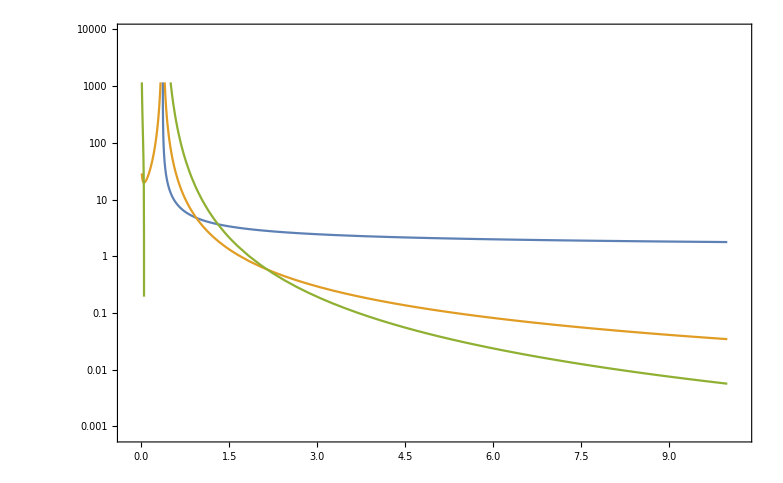

```mathematica
LogPlot[{RatioAnalytic,Abs[DRatioAnalytic],DDRatioAnalyic},{M,.01,10},Frame->True]
```

```mathematica
FullSimplify[DDRatioAnalyic]
```

$Aborted

```mathematica
NSolve[DDRatioAnalyic == RatioAnalytic,M,Reals]
```

FactorSquareFree::lrgexp: Exponent is out of bounds for function FactorSquareFree.

PolynomialGCD::lrgexp: Exponent is out of bounds for function PolynomialGCD.

NSolve[-(0.030704 (-0.322368/((1-1.28947 M^(1/4)) M^(3/4))+(0.322368 (1-0.024038 M^0.19))/((M-0.0202 M^1.19)^(3/4) (1-1.28947 (M-0.0202 M^1.19)^(1/4)))))/((1-0.0202 M^0.19) M^0.81 Log[1-0.0202 M^0.19]^2)-1/Log[1-0.0202 M^0.19]4 (0.241776/((1-1.28947 M^(1/4)) M^(7/4))-0.103921/((1-1.28947 M^(1/4))^2 M^(3/2))+(0.103921 (1-0.024038 M^0.19)^2)/((M-0.0202 M^1.19)^(3/2) (1-1.28947 (M-0.0202 M^1.19)^(1/4))^2)-(0.241776 (1-0.024038 M^0.19)^2)/((M-0.0202 M^1.19)^(7/4) (1-1.28947 (M-0.0202 M^1.19)^(1/4)))-0.00147233/(M^0.81 (M-0.0202 M^1.19)^(3/4) (1-1.28947 (M-0.0202 M^1.19)^(1/4))))-(0.000117842 (Log[1-1.28947 M^(1/4)]-Log[1-1.28947 (M-0.0202 M^1.19)^(1/4)]))/((1-0.0202 M^0.19)^2 M^1.62 Log[1-0.0202 M^0.19]^3)+(0.0124351 (Log[1-1.28947 M^(1/4)]-Log[1-1.28947 (M-0.0202 M^1.19)^(1/4)]))/((1-0.0202 M^0.19) M^1.81 Log[1-0.0202 M^0.19]^2)-(0.000058921 (Log[1-1.28947 M^(1/4)]-Log[1-1.28947 (M-0.0202 M^1.19)^(1/4)]))/((1-0.0202 M^0.19)^2 M^1.62 Log[1-0.0202 M^0.19]^2)==-(4 (Log[1-1.28947 M^(1/4)]-Log[1-1.28947 (M-0.0202 M^1.19)^(1/4)]))/Log[1-0.0202 M^0.19],M]

```mathematica
RatioSpecific=(
noise=0.2;
ParallelTable[
value=Re[Ratio/.{
M->i,
η->3/4,
γ->1.19,
f0->0.0202*(1+RandomReal[{-noise,noise}]),
B0->1.9*10^(-2)*(1+RandomReal[{-noise,noise}]),
Bm->0.0245*(1+RandomReal[{-noise,noise}])
}];
{i,value},
{i,0.1,10,0.00001}]
);
```

```mathematica
PosR=Select[RatioSpecific,#[[2]]>0&];
MAPosR=MovingAverage[PosR,100000];
```

```mathematica
AllometricAsymptotePlot=Show[{
ListLogPlot[PosR,Frame->True,PlotRange->{0,10},FrameLabel->{"Mass","σ/ρ"},PlotStyle->Directive[{Opacity[0.45]}]],
LogPlot[RatioAnalytic,{M,0.36784590002898243,10},PlotStyle->Black,PlotRange->All],
(*ListPlot[MAPosR,PlotStyle->Directive[{Dashed,ColorData[97,2]}]],*)
Graphics[{EdgeForm[Directive[Thick,ColorData[97,4]]],Directive[{Transparent}],Polygon[{{1.3,Log@0.05},{1.3,Log@9.95},{2.5,Log@9.95},{2.5,Log@0.05}}]}],
(*Graphics[{Dashed,Line[{{2.5,0},{2.5,10}}]}],*)
Graphics[Text[Style["Etruscan shrew",ColorData[97,4]],{3.75,Log@0.75}]],
Graphics[{Dashed,Black,Line[{{0.8029467083137317,Log@0.05},{0.8029467083137317,Log@9.95}}]}]
}]
```

-Graphics-

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_AlloAsymptote.jpg",AllometricAsymptotePlot,"JPG",ImageResolution->800]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_AlloAsymptote.jpg

```mathematica
starvation=-Bm/(Em*Log[1-f0*M^(γ-1)])
```

-Bm/(Em Log[1-f0 M^(-1+γ)])

```mathematica
growth= λ0*M^η2
```

M^η2 λ0

```mathematica
0.75-1
```

-0.25

```mathematica
-1/Log[1-M^-0.25]>M^-0.25
```

-1/Log[1-1/M^0.25]>1/M^0.25

```mathematica
Reduce[-1/Log[1-M^-0.25]>M^-0.25/.M->4]
```

True

```mathematica
1/M^0.25/.M->10
```

0.562341

Fixed points over mass

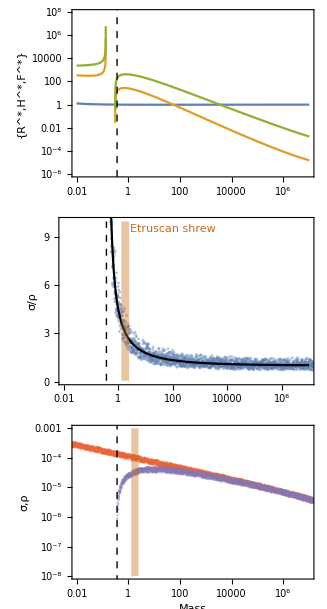

```mathematica
With[{
ts=1,
(*B0*)B0=1.9*10^(-2),
(*Bm*)Bm=0.0245,
(*Em*)Em=21.39/2*1000(*J/gram*),
(*η*)η=3/4,
(*η2*)η2=-0.206,
(*λ0*)λ0=3.3879*10^(-7),
(*ef*)ef=0.001,
(*γ*)γ=1.19,
(*ζ*)ζ=1.01,
(*f0*)f0=0.0202,
(*mm0*)mm0=0.324},
Rstar = (μ (-λ+σ))/(λ ρ+μ σ);
Hstar = (α λ^2 (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ));
Fstar = (α λ μ (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ));
growth =N[ts* λ0*M^η2];
starvation =  N[ts*-Bm/(Em*Log[1-f0*M^(γ-1)])];
mortality =N[ts*-Bm/(Em*Log[1-(f0*M^γ+ mm0*M^ζ)/M])];
recovery =N[ ts*- ((η-1)*Bm/Em)/(Log[1-(M*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])];
maintenance = ts*ef*B0*M^η;
resourcegrowth = ts*0.5;

Ratio = FullSimplify[starvation/recovery];
RatioSpecificAll=(
noise=0.2;
MassValues = RecurrenceTable[{Mass[n+1] == Mass[n]+1/100Mass[n],Mass[1]==0.0000001},Mass,{n,1,3500}];
ParallelTable[
sigmanoise=starvation*(1+RandomReal[{-noise,noise}])/.{M->i};
rhonoise = recovery*(1+RandomReal[{-noise,noise}])/.{M->i};
value=Re[sigmanoise/rhonoise];
{i,value,sigmanoise,rhonoise},
{i,MassValues}]
);
RatioSpecific = Transpose[{RatioSpecificAll[[All,1]],RatioSpecificAll[[All,2]]}];
SigmaSpecific = Transpose[{RatioSpecificAll[[All,1]],RatioSpecificAll[[All,3]]}];
RhoSpecific = Transpose[{RatioSpecificAll[[All,1]],RatioSpecificAll[[All,4]]}];
PosR=Select[RatioSpecific,#[[2]]>0&];
(*MAPosR=MovingAverage[PosR,100000];*)
RstarM = Rstar/.{α->resourcegrowth,λ->growth,σ->starvation,ρ->recovery,β->maintenance,μ->mortality};
HstarM = Hstar/.{α->resourcegrowth,λ->growth,σ->starvation,ρ->recovery,β->maintenance,μ->mortality};
FstarM = Fstar/.{α->resourcegrowth,λ->growth,σ->starvation,ρ->recovery,β->maintenance,μ->mortality};
(*FAsymptote = FindMaximum[FstarM,M];*)
MassLimit=0.36784590002898243;
FPSigmaRhoPlot=GraphicsColumn[{
Show[{
LogLogPlot[{RstarM,HstarM,FstarM},{M,0.01,10^7},Frame->True,FrameLabel->{None,"{R^*,H^*,F^*}"},PlotRange->{{0.01,10^7},All},FrameTicks->{False,True},ImageSize->300],
Graphics[{Dashed,Black,Line[{{Log@MassLimit,-100},{Log@MassLimit,Log@10^10}}]}]
}(*,ImagePadding->{{43,14},{Automatic,Automatic}}*)],
Show[{
ListLogLinearPlot[PosR,Frame->True,PlotRange->{{0.01,10^7},{0,10}},FrameLabel->{None,"σ/ρ"},FrameTicks->{False,True},PlotStyle->Directive[{Opacity[0.45]}],ImageSize->300],
LogLinearPlot[Ratio,{M,0.36784590002898243,10^7},PlotStyle->Black,PlotRange->All],
(*ListPlot[MAPosR,PlotStyle->Directive[{Dashed,ColorData[97,2]}]],*)
Graphics[{(*EdgeForm[Directive[Thick,ColorData[97,4]]],*)Directive[{ColorData[97,6],Opacity[0.4]}],Polygon[{{Log@1.3,0.05},{Log@1.3,9.95},{Log@2.5,9.95},{Log@2.5,0.05}}]}],
(*Graphics[{Dashed,Line[{{2.5,0},{2.5,10}}]}],*)
Graphics[Text[Style["Etruscan shrew",FontSize->Medium,ColorData[97,6]],{Log@100,9.5}]],
Graphics[{Dashed,Black,Line[{{Log@MassLimit,0.05},{Log@MassLimit,9.95}}]}]
}(*,ImagePadding->{{43,14},{Automatic,Automatic}}*)],
Show[{
ListLogLogPlot[Re[SigmaSpecific],PlotRange->{{0.01,10^7},{10^-8,10^-3}},Frame->True,FrameLabel->{"Mass","σ,ρ"},PlotStyle->Directive[{Opacity[0.3],ColorData[97,4]}],ImageSize->300],
ListLogLogPlot[Re[RhoSpecific],Frame->True,PlotStyle->Directive[{Opacity[0.3],ColorData[97,5]}]],
Graphics[{Dashed,Black,Line[{{Log@MassLimit,-100},{Log@MassLimit,Log@10^-3}}]}],
Graphics[{(*EdgeForm[Directive[Thick,ColorData[97,4]]],*)Directive[{ColorData[97,6],Opacity[0.4]}],Polygon[{{Log@1.3,Log@(10^-8)},{Log@1.3,Log@(10^-3)},{Log@2.5,Log@(10^-3)},{Log@2.5,Log@(10^-8)}}]}]
(*Graphics[{Dashed,Line[{{2.5,0},{2.5,10}}]}],*)
(*Graphics[Text[Style["Etruscan shrew",FontSize->Medium,ColorData[97,6]],{Log@40,Log@(10^-3.2)}]]*)
}(*,ImagePadding->{{43,0},{Automatic,Automatic}}*)]
}(*,ImagePadding->{{10,10},{200,110}}*)]
]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_FPAllometric.pdf",FPSigmaRhoPlot,"PDF",ImageResolution->300]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_FPAllometric.pdf

```mathematica
MassValues = RecurrenceTable[{Mass[n+1] == Mass[n]+1/100Mass[n],Mass[1]==0.0000001},Mass,{n,1,3500}]
```

{1.×10^-7,1.01×10^-7,1.0201×10^-7,1.0303×10^-7,1.0406×10^-7,1.05101×10^-7,1.06152×10^-7,1.07214×10^-7,1.08286×10^-7,1.09369×10^-7,1.10462×10^-7,1.11567×10^-7,1.12683×10^-7,1.13809×10^-7,1.14947×10^-7,1.16097×10^-7,1.17258×10^-7,1.1843×10^-7,1.19615×10^-7,1.20811×10^-7,1.22019×10^-7,1.23239×10^-7,1.24472×10^-7,1.25716×10^-7,1.26973×10^-7,1.28243×10^-7,1.29526×10^-7,1.30821×10^-7,1.32129×10^-7,1.3345×10^-7,1.34785×10^-7,1.36133×10^-7,1.37494×10^-7,1.38869×10^-7,1.40258×10^-7,1.4166×10^-7,1.43077×10^-7,1.44508×10^-7,1.45953×10^-7,1.47412×10^-7,1.48886×10^-7,1.50375×10^-7,1.51879×10^-7,1.53398×10^-7,1.54932×10^-7,1.56481×10^-7,1.58046×10^-7,1.59626×10^-7,1.61223×10^-7,1.62835×10^-7,1.64463×10^-7,1.66108×10^-7,1.67769×10^-7,1.69447×10^-7,1.71141×10^-7,1.72852×10^-7,1.74581×10^-7,1.76327×10^-7,1.7809×10^-7,1.79871×10^-7,1.8167×10^-7,1.83486×10^-7,1.85321×10^-7,1.87174×10^-7,1.89046×10^-7,1.90937×10^-7,1.92846×10^-7,1.94774×10^-7,1.96722×10^-7,1.98689×10^-7,2.00676×10^-7,2.02683×10^-7,2.0471×10^-7,2.06757×10^-7,2.08825×10^-7,2.10913×10^-7,2.13022×10^-7,2.15152×10^-7,2.17304×10^-7,2.19477×10^-7,2.21672×10^-7,2.23888×10^-7,2.26127×10^-7,2.28388×10^-7,2.30672×10^-7,2.32979×10^-7,2.35309×10^-7,2.37662×10^-7,2.40038×10^-7,2.42439×10^-7,2.44863×10^-7,2.47312×10^-7,2.49785×10^-7,2.52283×10^-7,2.54806×10^-7,2.57354×10^-7,2.59927×10^-7,2.62527×10^-7,2.65152×10^-7,2.67803×10^-7,2.70481×10^-7,2.73186×10^-7,2.75918×10^-7,2.78677×10^-7,2.81464×10^-7,2.84279×10^-7,2.87121×10^-7,2.89993×10^-7,2.92893×10^-7,2.95822×10^-7,2.9878×10^-7,3.01768×10^-7,3.04785×10^-7,3.07833×10^-7,3.10911×10^-7,3.1402×10^-7,3.17161×10^-7,3.20332×10^-7,3.23536×10^-7,3.26771×10^-7,3.30039×10^-7,3.33339×10^-7,3.36672×10^-7,3.40039×10^-7,3.4344×10^-7,3.46874×10^-7,3.50343×10^-7,3.53846×10^-7,3.57385×10^-7,3.60958×10^-7,3.64568×10^-7,3.68214×10^-7,3.71896×10^-7,3.75615×10^-7,3.79371×10^-7,3.83165×10^-7,3.86996×10^-7,3.90866×10^-7,3.94775×10^-7,3.98723×10^-7,4.0271×10^-7,4.06737×10^-7,4.10804×10^-7,4.14912×10^-7,4.19062×10^-7,4.23252×10^-7,4.27485×10^-7,4.3176×10^-7,4.36077×10^-7,4.40438×10^-7,4.44842×10^-7,4.49291×10^-7,4.53784×10^-7,4.58321×10^-7,4.62905×10^-7,4.67534×10^-7,4.72209×10^-7,4.76931×10^-7,4.817×10^-7,4.86517×10^-7,4.91383×10^-7,4.96296×10^-7,5.01259×10^-7,5.06272×10^-7,5.11335×10^-7,5.16448×10^-7,5.21613×10^-7,5.26829×10^-7,5.32097×10^-7,5.37418×10^-7,5.42792×10^-7,5.4822×10^-7,5.53702×10^-7,5.59239×10^-7,5.64832×10^-7,5.7048×10^-7,5.76185×10^-7,5.81947×10^-7,5.87766×10^-7,5.93644×10^-7,5.9958×10^-7,6.05576×10^-7,6.11632×10^-7,6.17748×10^-7,6.23926×10^-7,6.30165×10^-7,6.36466×10^-7,6.42831×10^-7,6.49259×10^-7,6.55752×10^-7,6.6231×10^-7,6.68933×10^-7,6.75622×10^-7,6.82378×10^-7,6.89202×10^-7,6.96094×10^-7,7.03055×10^-7,7.10085×10^-7,7.17186×10^-7,7.24358×10^-7,7.31602×10^-7,7.38918×10^-7,7.46307×10^-7,7.5377×10^-7,7.61308×10^-7,7.68921×10^-7,7.7661×10^-7,7.84376×10^-7,7.9222×10^-7,8.00142×10^-7,8.08144×10^-7,8.16225×10^-7,8.24387×10^-7,8.32631×10^-7,8.40957×10^-7,8.49367×10^-7,8.57861×10^-7,8.66439×10^-7,8.75104×10^-7,8.83855×10^-7,8.92693×10^-7,9.0162×10^-7,9.10636×10^-7,9.19743×10^-7,9.2894×10^-7,9.3823×10^-7,9.47612×10^-7,9.57088×10^-7,9.66659×10^-7,9.76325×10^-7,9.86089×10^-7,9.9595×10^-7,1.00591×10^-6,1.01597×10^-6,1.02613×10^-6,1.03639×10^-6,1.04675×10^-6,1.05722×10^-6,1.06779×10^-6,1.07847×10^-6,1.08926×10^-6,1.10015×10^-6,1.11115×10^-6,1.12226×10^-6,1.13348×10^-6,1.14482×10^-6,1.15627×10^-6,1.16783×10^-6,1.17951×10^-6,1.1913×10^-6,1.20322×10^-6,1.21525×10^-6,1.2274×10^-6,1.23967×10^-6,1.25207×10^-6,1.26459×10^-6,1.27724×10^-6,1.29001×10^-6,1.30291×10^-6,1.31594×10^-6,1.3291×10^-6,1.34239×10^-6,1.35581×10^-6,1.36937×10^-6,1.38307×10^-6,1.3969×10^-6,1.41086×10^-6,1.42497×10^-6,1.43922×10^-6,1.45362×10^-6,1.46815×10^-6,1.48283×10^-6,1.49766×10^-6,1.51264×10^-6,1.52776×10^-6,1.54304×10^-6,1.55847×10^-6,1.57406×10^-6,1.5898×10^-6,1.6057×10^-6,1.62175×10^-6,1.63797×10^-6,1.65435×10^-6,1.67089×10^-6,1.6876×10^-6,1.70448×10^-6,1.72152×10^-6,1.73874×10^-6,1.75613×10^-6,1.77369×10^-6,1.79142×10^-6,1.80934×10^-6,1.82743×10^-6,1.84571×10^-6,1.86416×10^-6,1.8828×10^-6,1.90163×10^-6,1.92065×10^-6,1.93986×10^-6,1.95925×10^-6,1.97885×10^-6,1.99864×10^-6,2.01862×10^-6,2.03881×10^-6,2.0592×10^-6,2.07979×10^-6,2.10059×10^-6,2.12159×10^-6,2.14281×10^-6,2.16424×10^-6,2.18588×10^-6,2.20774×10^-6,2.22981×10^-6,2.25211×10^-6,2.27463×10^-6,2.29738×10^-6,2.32035×10^-6,2.34356×10^-6,2.36699×10^-6,2.39066×10^-6,2.41457×10^-6,2.43871×10^-6,2.4631×10^-6,2.48773×10^-6,2.51261×10^-6,2.53774×10^-6,2.56311×10^-6,2.58874×10^-6,2.61463×10^-6,2.64078×10^-6,2.66719×10^-6,2.69386×10^-6,2.7208×10^-6,2.748×10^-6,2.77548×10^-6,2.80324×10^-6,2.83127×10^-6,2.85958×10^-6,2.88818×10^-6,2.91706×10^-6,2.94623×10^-6,2.9757×10^-6,3.00545×10^-6,3.03551×10^-6,3.06586×10^-6,3.09652×10^-6,3.12749×10^-6,3.15876×10^-6,3.19035×10^-6,3.22225×10^-6,3.25447×10^-6,3.28702×10^-6,3.31989×10^-6,3.35309×10^-6,3.38662×10^-6,3.42049×10^-6,3.45469×10^-6,3.48924×10^-6,3.52413×10^-6,3.55937×10^-6,3.59496×10^-6,3.63091×10^-6,3.66722×10^-6,3.7039×10^-6,3.74093×10^-6,3.77834×10^-6,3.81613×10^-6,3.85429×10^-6,3.89283×10^-6,3.93176×10^-6,3.97108×10^-6,4.01079×10^-6,4.0509×10^-6,4.0914×10^-6,4.13232×10^-6,4.17364×10^-6,4.21538×10^-6,4.25753×10^-6,4.30011×10^-6,4.34311×10^-6,4.38654×10^-6,4.4304×10^-6,4.47471×10^-6,4.51946×10^-6,4.56465×10^-6,4.6103×10^-6,4.6564×10^-6,4.70296×10^-6,4.74999×10^-6,4.79749×10^-6,4.84547×10^-6,4.89392×10^-6,4.94286×10^-6,4.99229×10^-6,5.04221×10^-6,5.09264×10^-6,5.14356×10^-6,5.195×10^-6,5.24695×10^-6,5.29942×10^-6,5.35241×10^-6,5.40594×10^-6,5.46×10^-6,5.5146×10^-6,5.56974×10^-6,5.62544×10^-6,5.68169×10^-6,5.73851×10^-6,5.79589×10^-6,5.85385×10^-6,5.91239×10^-6,5.97152×10^-6,6.03123×10^-6,6.09154×10^-6,6.15246×10^-6,6.21398×10^-6,6.27612×10^-6,6.33888×10^-6,6.40227×10^-6,6.4663×10^-6,6.53096×10^-6,6.59627×10^-6,6.66223×10^-6,6.72885×10^-6,6.79614×10^-6,6.8641×10^-6,6.93275×10^-6,7.00207×10^-6,7.07209×10^-6,7.14281×10^-6,7.21424×10^-6,7.28638×10^-6,7.35925×10^-6,7.43284×10^-6,7.50717×10^-6,7.58224×10^-6,7.65806×10^-6,7.73464×10^-6,7.81199×10^-6,7.89011×10^-6,7.96901×10^-6,8.0487×10^-6,8.12919×10^-6,8.21048×10^-6,8.29259×10^-6,8.37551×10^-6,8.45927×10^-6,8.54386×10^-6,8.6293×10^-6,8.71559×10^-6,8.80275×10^-6,8.89077×10^-6,8.97968×10^-6,9.06948×10^-6,9.16017×10^-6,9.25178×10^-6,9.34429×10^-6,9.43774×10^-6,9.53211×10^-6,9.62743×10^-6,9.72371×10^-6,9.82095×10^-6,9.91916×10^-6,0.0000100183,0.0000101185,0.0000102197,0.0000103219,0.0000104251,0.0000105294,0.0000106347,0.000010741,0.0000108484,0.0000109569,0.0000110665,0.0000111772,0.0000112889,0.0000114018,0.0000115158,0.000011631,0.0000117473,0.0000118648,0.0000119834,0.0000121033,0.0000122243,0.0000123465,0.00001247,0.0000125947,0.0000127206,0.0000128478,0.0000129763,0.0000131061,0.0000132372,0.0000133695,0.0000135032,0.0000136383,0.0000137746,0.0000139124,0.0000140515,0.000014192,0.0000143339,0.0000144773,0.0000146221,0.0000147683,0.000014916,0.0000150651,0.0000152158,0.0000153679,0.0000155216,0.0000156768,0.0000158336,0.0000159919,0.0000161518,0.0000163134,0.0000164765,0.0000166413,0.0000168077,0.0000169757,0.0000171455,0.000017317,0.0000174901,0.000017665,0.0000178417,0.0000180201,0.0000182003,0.0000183823,0.0000185661,0.0000187518,0.0000189393,0.0000191287,0.00001932,0.0000195132,0.0000197083,0.0000199054,0.0000201045,0.0000203055,0.0000205086,0.0000207136,0.0000209208,0.00002113,0.0000213413,0.0000215547,0.0000217702,0.0000219879,0.0000222078,0.0000224299,0.0000226542,0.0000228807,0.0000231095,0.0000233406,0.0000235741,0.0000238098,0.0000240479,0.0000242884,0.0000245313,0.0000247766,0.0000250243,0.0000252746,0.0000255273,0.0000257826,0.0000260404,0.0000263008,0.0000265638,0.0000268295,0.0000270978,0.0000273687,0.0000276424,0.0000279189,0.000028198,0.00002848,0.0000287648,0.0000290525,0.000029343,0.0000296364,0.0000299328,0.0000302321,0.0000305344,0.0000308398,0.0000311482,0.0000314597,0.0000317743,0.000032092,0.0000324129,0.000032737,0.0000330644,0.0000333951,0.000033729,0.0000340663,0.000034407,0.000034751,0.0000350985,0.0000354495,0.000035804,0.0000361621,0.0000365237,0.0000368889,0.0000372578,0.0000376304,0.0000380067,0.0000383868,0.0000387706,0.0000391583,0.0000395499,0.0000399454,0.0000403449,0.0000407483,0.0000411558,0.0000415674,0.000041983,0.0000424029,0.0000428269,0.0000432552,0.0000436877,0.0000441246,0.0000445658,0.0000450115,0.0000454616,0.0000459162,0.0000463754,0.0000468391,0.0000473075,0.0000477806,0.0000482584,0.000048741,0.0000492284,0.0000497207,0.0000502179,0.0000507201,0.0000512273,0.0000517396,0.000052257,0.0000527795,0.0000533073,0.0000538404,0.0000543788,0.0000549226,0.0000554718,0.0000560265,0.0000565868,0.0000571527,0.0000577242,0.0000583014,0.0000588844,0.0000594733,0.000060068,0.0000606687,0.0000612754,0.0000618881,0.000062507,0.0000631321,0.0000637634,0.0000644011,0.0000650451,0.0000656955,0.0000663525,0.000067016,0.0000676862,0.000068363,0.0000690466,0.0000697371,0.0000704345,0.0000711388,0.0000718502,0.0000725687,0.0000732944,0.0000740273,0.0000747676,0.0000755153,0.0000762705,0.0000770332,0.0000778035,0.0000785815,0.0000793673,0.000080161,0.0000809626,0.0000817722,0.00008259,0.0000834159,0.00008425,0.0000850925,0.0000859435,0.0000868029,0.0000876709,0.0000885476,0.0000894331,0.0000903274,0.0000912307,0.000092143,0.0000930644,0.0000939951,0.000094935,0.0000958844,0.0000968432,0.0000978117,0.0000987898,0.0000997777,0.000100775,0.000101783,0.000102801,0.000103829,0.000104867,0.000105916,0.000106975,0.000108045,0.000109125,0.000110217,0.000111319,0.000112432,0.000113556,0.000114692,0.000115839,0.000116997,0.000118167,0.000119349,0.000120542,0.000121748,0.000122965,0.000124195,0.000125437,0.000126691,0.000127958,0.000129238,0.00013053,0.000131835,0.000133154,0.000134485,0.00013583,0.000137188,0.00013856,0.000139946,0.000141345,0.000142759,0.000144186,0.000145628,0.000147085,0.000148555,0.000150041,0.000151541,0.000153057,0.000154587,0.000156133,0.000157695,0.000159271,0.000160864,0.000162473,0.000164098,0.000165739,0.000167396,0.00016907,0.000170761,0.000172468,0.000174193,0.000175935,0.000177694,0.000179471,0.000181266,0.000183078,0.000184909,0.000186758,0.000188626,0.000190512,0.000192417,0.000194341,0.000196285,0.000198248,0.00020023,0.000202232,0.000204255,0.000206297,0.00020836,0.000210444,0.000212548,0.000214674,0.000216821,0.000218989,0.000221179,0.00022339,0.000225624,0.000227881,0.000230159,0.000232461,0.000234786,0.000237134,0.000239505,0.0002419,0.000244319,0.000246762,0.00024923,0.000251722,0.000254239,0.000256782,0.000259349,0.000261943,0.000264562,0.000267208,0.00026988,0.000272579,0.000275305,0.000278058,0.000280838,0.000283647,0.000286483,0.000289348,0.000292241,0.000295164,0.000298115,0.000301097,0.000304108,0.000307149,0.00031022,0.000313322,0.000316456,0.00031962,0.000322816,0.000326045,0.000329305,0.000332598,0.000335924,0.000339283,0.000342676,0.000346103,0.000349564,0.000353059,0.00035659,0.000360156,0.000363758,0.000367395,0.000371069,0.00037478,0.000378528,0.000382313,0.000386136,0.000389997,0.000393897,0.000397836,0.000401815,0.000405833,0.000409891,0.00041399,0.00041813,0.000422311,0.000426534,0.0004308,0.000435108,0.000439459,0.000443853,0.000448292,0.000452775,0.000457303,0.000461876,0.000466494,0.000471159,0.000475871,0.00048063,0.000485436,0.00049029,0.000495193,0.000500145,0.000505146,0.000510198,0.0005153,0.000520453,0.000525657,0.000530914,0.000536223,0.000541585,0.000547001,0.000552471,0.000557996,0.000563576,0.000569212,0.000574904,0.000580653,0.000586459,0.000592324,0.000598247,0.00060423,0.000610272,0.000616375,0.000622538,0.000628764,0.000635051,0.000641402,0.000647816,0.000654294,0.000660837,0.000667445,0.00067412,0.000680861,0.00068767,0.000694546,0.000701492,0.000708507,0.000715592,0.000722748,0.000729975,0.000737275,0.000744648,0.000752094,0.000759615,0.000767211,0.000774883,0.000782632,0.000790459,0.000798363,0.000806347,0.00081441,0.000822554,0.00083078,0.000839088,0.000847479,0.000855953,0.000864513,0.000873158,0.00088189,0.000890709,0.000899616,0.000908612,0.000917698,0.000926875,0.000936144,0.000945505,0.00095496,0.00096451,0.000974155,0.000983896,0.000993735,0.00100367,0.00101371,0.00102385,0.00103409,0.00104443,0.00105487,0.00106542,0.00107607,0.00108683,0.0010977,0.00110868,0.00111977,0.00113096,0.00114227,0.0011537,0.00116523,0.00117689,0.00118865,0.00120054,0.00121255,0.00122467,0.00123692,0.00124929,0.00126178,0.0012744,0.00128714,0.00130001,0.00131301,0.00132614,0.00133941,0.0013528,0.00136633,0.00137999,0.00139379,0.00140773,0.00142181,0.00143602,0.00145038,0.00146489,0.00147954,0.00149433,0.00150928,0.00152437,0.00153961,0.00155501,0.00157056,0.00158626,0.00160213,0.00161815,0.00163433,0.00165067,0.00166718,0.00168385,0.00170069,0.0017177,0.00173487,0.00175222,0.00176974,0.00178744,0.00180532,0.00182337,0.0018416,0.00186002,0.00187862,0.00189741,0.00191638,0.00193554,0.0019549,0.00197445,0.00199419,0.00201413,0.00203427,0.00205462,0.00207516,0.00209592,0.00211687,0.00213804,0.00215942,0.00218102,0.00220283,0.00222486,0.00224711,0.00226958,0.00229227,0.00231519,0.00233835,0.00236173,0.00238535,0.0024092,0.00243329,0.00245763,0.0024822,0.00250702,0.00253209,0.00255742,0.00258299,0.00260882,0.00263491,0.00266126,0.00268787,0.00271475,0.0027419,0.00276931,0.00279701,0.00282498,0.00285323,0.00288176,0.00291058,0.00293968,0.00296908,0.00299877,0.00302876,0.00305905,0.00308964,0.00312053,0.00315174,0.00318326,0.00321509,0.00324724,0.00327971,0.00331251,0.00334563,0.00337909,0.00341288,0.00344701,0.00348148,0.00351629,0.00355146,0.00358697,0.00362284,0.00365907,0.00369566,0.00373262,0.00376994,0.00380764,0.00384572,0.00388418,0.00392302,0.00396225,0.00400187,0.00404189,0.00408231,0.00412313,0.00416436,0.00420601,0.00424807,0.00429055,0.00433345,0.00437679,0.00442056,0.00446476,0.00450941,0.0045545,0.00460005,0.00464605,0.00469251,0.00473943,0.00478683,0.0048347,0.00488304,0.00493187,0.00498119,0.005031,0.00508131,0.00513213,0.00518345,0.00523528,0.00528764,0.00534051,0.00539392,0.00544786,0.00550234,0.00555736,0.00561293,0.00566906,0.00572575,0.00578301,0.00584084,0.00589925,0.00595824,0.00601782,0.006078,0.00613878,0.00620017,0.00626217,0.00632479,0.00638804,0.00645192,0.00651644,0.0065816,0.00664742,0.00671389,0.00678103,0.00684884,0.00691733,0.00698651,0.00705637,0.00712693,0.0071982,0.00727019,0.00734289,0.00741632,0.00749048,0.00756538,0.00764104,0.00771745,0.00779462,0.00787257,0.0079513,0.00803081,0.00811112,0.00819223,0.00827415,0.00835689,0.00844046,0.00852486,0.00861011,0.00869621,0.00878318,0.00887101,0.00895972,0.00904932,0.00913981,0.00923121,0.00932352,0.00941675,0.00951092,0.00960603,0.00970209,0.00979911,0.0098971,0.00999607,0.010096,0.010197,0.010299,0.010402,0.010506,0.010611,0.0107171,0.0108243,0.0109326,0.0110419,0.0111523,0.0112638,0.0113765,0.0114902,0.0116051,0.0117212,0.0118384,0.0119568,0.0120763,0.0121971,0.0123191,0.0124423,0.0125667,0.0126924,0.0128193,0.0129475,0.013077,0.0132077,0.0133398,0.0134732,0.0136079,0.013744,0.0138814,0.0140203,0.0141605,0.0143021,0.0144451,0.0145895,0.0147354,0.0148828,0.0150316,0.0151819,0.0153338,0.0154871,0.015642,0.0157984,0.0159564,0.0161159,0.0162771,0.0164399,0.0166043,0.0167703,0.016938,0.0171074,0.0172785,0.0174512,0.0176258,0.017802,0.01798,0.0181598,0.0183414,0.0185248,0.0187101,0.0188972,0.0190862,0.019277,0.0194698,0.0196645,0.0198611,0.0200598,0.0202604,0.020463,0.0206676,0.0208743,0.021083,0.0212938,0.0215068,0.0217218,0.0219391,0.0221584,0.02238,0.0226038,0.0228299,0.0230582,0.0232888,0.0235216,0.0237569,0.0239944,0.0242344,0.0244767,0.0247215,0.0249687,0.0252184,0.0254706,0.0257253,0.0259825,0.0262423,0.0265048,0.0267698,0.0270375,0.0273079,0.027581,0.0278568,0.0281354,0.0284167,0.0287009,0.0289879,0.0292778,0.0295705,0.0298662,0.0301649,0.0304666,0.0307712,0.0310789,0.0313897,0.0317036,0.0320207,0.0323409,0.0326643,0.0329909,0.0333208,0.033654,0.0339906,0.0343305,0.0346738,0.0350205,0.0353707,0.0357244,0.0360817,0.0364425,0.0368069,0.037175,0.0375467,0.0379222,0.0383014,0.0386844,0.0390713,0.039462,0.0398566,0.0402552,0.0406577,0.0410643,0.041475,0.0418897,0.0423086,0.0427317,0.043159,0.0435906,0.0440265,0.0444668,0.0449114,0.0453605,0.0458142,0.0462723,0.046735,0.0472024,0.0476744,0.0481511,0.0486326,0.049119,0.0496102,0.0501063,0.0506073,0.0511134,0.0516245,0.0521408,0.0526622,0.0531888,0.0537207,0.0542579,0.0548005,0.0553485,0.055902,0.056461,0.0570256,0.0575959,0.0581718,0.0587535,0.0593411,0.0599345,0.0605338,0.0611392,0.0617506,0.0623681,0.0629917,0.0636217,0.0642579,0.0649005,0.0655495,0.066205,0.066867,0.0675357,0.068211,0.0688931,0.0695821,0.0702779,0.0709807,0.0716905,0.0724074,0.0731315,0.0738628,0.0746014,0.0753474,0.0761009,0.0768619,0.0776305,0.0784068,0.0791909,0.0799828,0.0807826,0.0815905,0.0824064,0.0832304,0.0840627,0.0849034,0.0857524,0.0866099,0.087476,0.0883508,0.0892343,0.0901266,0.0910279,0.0919382,0.0928575,0.0937861,0.094724,0.0956712,0.0966279,0.0975942,0.0985702,0.0995559,0.100551,0.101557,0.102572,0.103598,0.104634,0.105681,0.106737,0.107805,0.108883,0.109972,0.111071,0.112182,0.113304,0.114437,0.115581,0.116737,0.117904,0.119083,0.120274,0.121477,0.122692,0.123919,0.125158,0.12641,0.127674,0.12895,0.13024,0.131542,0.132858,0.134186,0.135528,0.136883,0.138252,0.139635,0.141031,0.142441,0.143866,0.145304,0.146758,0.148225,0.149707,0.151204,0.152716,0.154244,0.155786,0.157344,0.158917,0.160507,0.162112,0.163733,0.16537,0.167024,0.168694,0.170381,0.172085,0.173806,0.175544,0.177299,0.179072,0.180863,0.182671,0.184498,0.186343,0.188207,0.190089,0.19199,0.193909,0.195848,0.197807,0.199785,0.201783,0.203801,0.205839,0.207897,0.209976,0.212076,0.214197,0.216339,0.218502,0.220687,0.222894,0.225123,0.227374,0.229648,0.231944,0.234264,0.236606,0.238972,0.241362,0.243776,0.246213,0.248676,0.251162,0.253674,0.256211,0.258773,0.261361,0.263974,0.266614,0.26928,0.271973,0.274693,0.27744,0.280214,0.283016,0.285846,0.288705,0.291592,0.294508,0.297453,0.300427,0.303432,0.306466,0.30953,0.312626,0.315752,0.31891,0.322099,0.32532,0.328573,0.331859,0.335177,0.338529,0.341914,0.345333,0.348787,0.352275,0.355797,0.359355,0.362949,0.366578,0.370244,0.373947,0.377686,0.381463,0.385277,0.38913,0.393022,0.396952,0.400921,0.404931,0.40898,0.41307,0.4172,0.421372,0.425586,0.429842,0.43414,0.438482,0.442867,0.447295,0.451768,0.456286,0.460849,0.465457,0.470112,0.474813,0.479561,0.484357,0.4892,0.494092,0.499033,0.504023,0.509064,0.514154,0.519296,0.524489,0.529734,0.535031,0.540381,0.545785,0.551243,0.556755,0.562323,0.567946,0.573626,0.579362,0.585156,0.591007,0.596917,0.602886,0.608915,0.615004,0.621154,0.627366,0.63364,0.639976,0.646376,0.65284,0.659368,0.665962,0.672621,0.679347,0.686141,0.693002,0.699932,0.706932,0.714001,0.721141,0.728352,0.735636,0.742992,0.750422,0.757926,0.765506,0.773161,0.780892,0.788701,0.796588,0.804554,0.8126,0.820726,0.828933,0.837222,0.845595,0.85405,0.862591,0.871217,0.879929,0.888728,0.897616,0.906592,0.915658,0.924814,0.934062,0.943403,0.952837,0.962365,0.971989,0.981709,0.991526,1.00144,1.01146,1.02157,1.03179,1.0421,1.05252,1.06305,1.07368,1.08442,1.09526,1.10621,1.11728,1.12845,1.13973,1.15113,1.16264,1.17427,1.18601,1.19787,1.20985,1.22195,1.23417,1.24651,1.25898,1.27156,1.28428,1.29712,1.31009,1.3232,1.33643,1.34979,1.36329,1.37692,1.39069,1.4046,1.41864,1.43283,1.44716,1.46163,1.47625,1.49101,1.50592,1.52098,1.53619,1.55155,1.56707,1.58274,1.59856,1.61455,1.6307,1.647,1.66347,1.68011,1.69691,1.71388,1.73102,1.74833,1.76581,1.78347,1.8013,1.81932,1.83751,1.85588,1.87444,1.89319,1.91212,1.93124,1.95055,1.97006,1.98976,2.00966,2.02975,2.05005,2.07055,2.09126,2.11217,2.13329,2.15462,2.17617,2.19793,2.21991,2.24211,2.26453,2.28718,2.31005,2.33315,2.35648,2.38004,2.40384,2.42788,2.45216,2.47668,2.50145,2.52647,2.55173,2.57725,2.60302,2.62905,2.65534,2.68189,2.70871,2.7358,2.76316,2.79079,2.8187,2.84688,2.87535,2.90411,2.93315,2.96248,2.9921,3.02202,3.05225,3.08277,3.1136,3.14473,3.17618,3.20794,3.24002,3.27242,3.30514,3.3382,3.37158,3.40529,3.43935,3.47374,3.50848,3.54356,3.579,3.61479,3.65094,3.68744,3.72432,3.76156,3.79918,3.83717,3.87554,3.9143,3.95344,3.99297,4.0329,4.07323,4.11397,4.1551,4.19666,4.23862,4.28101,4.32382,4.36706,4.41073,4.45483,4.49938,4.54438,4.58982,4.63572,4.68208,4.7289,4.77619,4.82395,4.87219,4.92091,4.97012,5.01982,5.07002,5.12072,5.17192,5.22364,5.27588,5.32864,5.38193,5.43574,5.4901,5.545,5.60045,5.65646,5.71302,5.77015,5.82785,5.88613,5.94499,6.00444,6.06449,6.12513,6.18638,6.24825,6.31073,6.37384,6.43758,6.50195,6.56697,6.63264,6.69897,6.76596,6.83362,6.90195,6.97097,7.04068,7.11109,7.1822,7.25402,7.32656,7.39983,7.47383,7.54857,7.62405,7.70029,7.77729,7.85507,7.93362,8.01295,8.09308,8.17401,8.25575,8.33831,8.4217,8.50591,8.59097,8.67688,8.76365,8.85129,8.9398,9.0292,9.11949,9.21068,9.30279,9.39582,9.48978,9.58467,9.68052,9.77733,9.8751,9.97385,10.0736,10.1743,10.2761,10.3788,10.4826,10.5874,10.6933,10.8003,10.9083,11.0173,11.1275,11.2388,11.3512,11.4647,11.5793,11.6951,11.8121,11.9302,12.0495,12.17,12.2917,12.4146,12.5388,12.6641,12.7908,12.9187,13.0479,13.1784,13.3101,13.4432,13.5777,13.7135,13.8506,13.9891,14.129,14.2703,14.413,14.5571,14.7027,14.8497,14.9982,15.1482,15.2997,15.4527,15.6072,15.7633,15.9209,16.0801,16.2409,16.4033,16.5673,16.733,16.9003,17.0694,17.24,17.4124,17.5866,17.7624,17.9401,18.1195,18.3007,18.4837,18.6685,18.8552,19.0437,19.2342,19.4265,19.6208,19.817,20.0152,20.2153,20.4175,20.6216,20.8279,21.0361,21.2465,21.459,21.6735,21.8903,22.1092,22.3303,22.5536,22.7791,23.0069,23.237,23.4693,23.704,23.9411,24.1805,24.4223,24.6665,24.9132,25.1623,25.4139,25.6681,25.9248,26.184,26.4458,26.7103,26.9774,27.2472,27.5197,27.7949,28.0728,28.3535,28.6371,28.9234,29.2127,29.5048,29.7998,30.0978,30.3988,30.7028,31.0098,31.3199,31.6331,31.9495,32.269,32.5917,32.9176,33.2467,33.5792,33.915,34.2542,34.5967,34.9427,35.2921,35.645,36.0015,36.3615,36.7251,37.0923,37.4633,37.8379,38.2163,38.5984,38.9844,39.3743,39.768,40.1657,40.5673,40.973,41.3827,41.7966,42.2145,42.6367,43.0631,43.4937,43.9286,44.3679,44.8116,45.2597,45.7123,46.1694,46.6311,47.0974,47.5684,48.0441,48.5245,49.0098,49.4999,49.9949,50.4948,50.9998,51.5098,52.0249,52.5451,53.0706,53.6013,54.1373,54.6787,55.2254,55.7777,56.3355,56.8988,57.4678,58.0425,58.6229,59.2091,59.8012,60.3992,61.0032,61.6133,62.2294,62.8517,63.4802,64.115,64.7562,65.4037,66.0578,66.7183,67.3855,68.0594,68.74,69.4274,70.1217,70.8229,71.5311,72.2464,72.9689,73.6986,74.4355,75.1799,75.9317,76.691,77.4579,78.2325,79.0148,79.805,80.603,81.4091,82.2232,83.0454,83.8758,84.7146,85.5617,86.4174,87.2815,88.1543,89.0359,89.9262,90.8255,91.7338,92.6511,93.5776,94.5134,95.4585,96.4131,97.3772,98.351,99.3345,100.328,101.331,102.344,103.368,104.402,105.446,106.5,107.565,108.641,109.727,110.824,111.933,113.052,114.182,115.324,116.478,117.642,118.819,120.007,121.207,122.419,123.643,124.88,126.128,127.39,128.664,129.95,131.25,132.562,133.888,135.227,136.579,137.945,139.324,140.718,142.125,143.546,144.981,146.431,147.896,149.375,150.868,152.377,153.901,155.44,156.994,158.564,160.15,161.751,163.369,165.002,166.652,168.319,170.002,171.702,173.419,175.153,176.905,178.674,180.461,182.265,184.088,185.929,187.788,189.666,191.563,193.478,195.413,197.367,199.341,201.334,203.348,205.381,207.435,209.509,211.604,213.72,215.858,218.016,220.196,222.398,224.622,226.869,229.137,231.429,233.743,236.08,238.441,240.826,243.234,245.666,248.123,250.604,253.11,255.641,258.198,260.78,263.387,266.021,268.681,271.368,274.082,276.823,279.591,282.387,285.211,288.063,290.943,293.853,296.791,299.759,302.757,305.784,308.842,311.931,315.05,318.201,321.383,324.596,327.842,331.121,334.432,337.776,341.154,344.566,348.011,351.491,355.006,358.556,362.142,365.763,369.421,373.115,376.846,380.615,384.421,388.265,392.148,396.069,400.03,404.03,408.071,412.151,416.273,420.436,424.64,428.886,433.175,437.507,441.882,446.301,450.764,455.271,459.824,464.422,469.067,473.757,478.495,483.28,488.113,492.994,497.924,502.903,507.932,513.011,518.141,523.323,528.556,533.842,539.18,544.572,550.017,555.518,561.073,566.684,572.35,578.074,583.855,589.693,595.59,601.546,607.561,613.637,619.773,625.971,632.231,638.553,644.939,651.388,657.902,664.481,671.126,677.837,684.616,691.462,698.376,705.36,712.414,719.538,726.733,734.,741.34,748.754,756.241,763.804,771.442,779.156,786.948,794.817,802.766,810.793,818.901,827.09,835.361,843.715,852.152,860.673,869.28,877.973,886.753,895.62,904.576,913.622,922.758,931.986,941.306,950.719,960.226,969.828,979.526,989.322,999.215,1009.21,1019.3,1029.49,1039.79,1050.18,1060.69,1071.29,1082.01,1092.83,1103.75,1114.79,1125.94,1137.2,1148.57,1160.06,1171.66,1183.37,1195.21,1207.16,1219.23,1231.42,1243.74,1256.18,1268.74,1281.43,1294.24,1307.18,1320.25,1333.46,1346.79,1360.26,1373.86,1387.6,1401.48,1415.49,1429.65,1443.94,1458.38,1472.97,1487.69,1502.57,1517.6,1532.77,1548.1,1563.58,1579.22,1595.01,1610.96,1627.07,1643.34,1659.77,1676.37,1693.14,1710.07,1727.17,1744.44,1761.88,1779.5,1797.3,1815.27,1833.42,1851.76,1870.28,1888.98,1907.87,1926.95,1946.22,1965.68,1985.33,2005.19,2025.24,2045.49,2065.95,2086.61,2107.47,2128.55,2149.83,2171.33,2193.04,2214.98,2237.12,2259.5,2282.09,2304.91,2327.96,2351.24,2374.75,2398.5,2422.49,2446.71,2471.18,2495.89,2520.85,2546.06,2571.52,2597.23,2623.2,2649.44,2675.93,2702.69,2729.72,2757.01,2784.58,2812.43,2840.55,2868.96,2897.65,2926.63,2955.89,2985.45,3015.31,3045.46,3075.91,3106.67,3137.74,3169.12,3200.81,3232.82,3265.14,3297.8,3330.77,3364.08,3397.72,3431.7,3466.02,3500.68,3535.68,3571.04,3606.75,3642.82,3679.25,3716.04,3753.2,3790.73,3828.64,3866.93,3905.59,3944.65,3984.1,4023.94,4064.18,4104.82,4145.87,4187.33,4229.2,4271.49,4314.21,4357.35,4400.92,4444.93,4489.38,4534.27,4579.62,4625.41,4671.67,4718.38,4765.57,4813.22,4861.36,4909.97,4959.07,5008.66,5058.75,5109.33,5160.43,5212.03,5264.15,5316.79,5369.96,5423.66,5477.9,5532.68,5588.,5643.88,5700.32,5757.32,5814.9,5873.05,5931.78,5991.1,6051.01,6111.52,6172.63,6234.36,6296.7,6359.67,6423.26,6487.5,6552.37,6617.9,6684.08,6750.92,6818.43,6886.61,6955.48,7025.03,7095.28,7166.23,7237.9,7310.27,7383.38,7457.21,7531.78,7607.1,7683.17,7760.,7837.6,7915.98,7995.14,8075.09,8155.84,8237.4,8319.77,8402.97,8487.,8571.87,8657.59,8744.17,8831.61,8919.92,9009.12,9099.21,9190.21,9282.11,9374.93,9468.68,9563.37,9659.,9755.59,9853.15,9951.68,10051.2,10151.7,10253.2,10355.8,10459.3,10563.9,10669.5,10776.2,10884.,10992.8,11102.8,11213.8,11325.9,11439.2,11553.6,11669.1,11785.8,11903.7,12022.7,12142.9,12264.4,12387.,12510.9,12636.,12762.3,12890.,13018.9,13149.1,13280.6,13413.4,13547.5,13683.,13819.8,13958.,14097.6,14238.5,14380.9,14524.7,14670.,14816.7,14964.9,15114.5,15265.7,15418.3,15572.5,15728.2,15885.5,16044.4,16204.8,16366.8,16530.5,16695.8,16862.8,17031.4,17201.7,17373.7,17547.5,17722.9,17900.2,18079.2,18260.,18442.6,18627.,18813.3,19001.4,19191.4,19383.3,19577.2,19772.9,19970.7,20170.4,20372.1,20575.8,20781.6,20989.4,21199.3,21411.3,21625.4,21841.6,22060.,22280.6,22503.4,22728.5,22955.8,23185.3,23417.2,23651.3,23887.9,24126.7,24368.,24611.7,24857.8,25106.4,25357.4,25611.,25867.1,26125.8,26387.1,26650.9,26917.4,27186.6,27458.5,27733.1,28010.4,28290.5,28573.4,28859.1,29147.7,29439.2,29733.6,30030.9,30331.2,30634.6,30940.9,31250.3,31562.8,31878.4,32197.2,32519.2,32844.4,33172.8,33504.6,33839.6,34178.,34519.8,34865.,35213.6,35565.8,35921.4,36280.6,36643.4,37009.9,37380.,37753.8,38131.3,38512.6,38897.8,39286.7,39679.6,40076.4,40477.2,40881.9,41290.7,41703.7,42120.7,42541.9,42967.3,43397.,43831.,44269.3,44712.,45159.1,45610.7,46066.8,46527.4,46992.7,47462.6,47937.3,48416.6,48900.8,49389.8,49883.7,50382.6,50886.4,51395.2,51909.2,52428.3,52952.6,53482.1,54016.9,54557.1,55102.7,55653.7,56210.2,56772.3,57340.,57913.4,58492.6,59077.5,59668.3,60265.,60867.6,61476.3,62091.1,62712.,63339.1,63972.5,64612.2,65258.3,65910.9,66570.,67235.7,67908.1,68587.2,69273.,69965.8,70665.4,71372.1,72085.8,72806.6,73534.7,74270.1,75012.8,75762.9,76520.5,77285.7,78058.6,78839.2,79627.6,80423.8,81228.1,82040.4,82860.8,83689.4,84526.3,85371.5,86225.2,87087.5,87958.4,88837.9,89726.3,90623.6,91529.8,92445.1,93369.6,94303.3,95246.3,96198.8,97160.8,98132.4,99113.7,100105.,101106.,102117.,103138.,104169.,105211.,106263.,107326.,108399.,109483.,110578.,111684.,112801.,113929.,115068.,116219.,117381.,118555.,119740.,120938.,122147.,123368.,124602.,125848.,127107.,128378.,129661.,130958.,132268.,133590.,134926.,136275.,137638.,139015.,140405.,141809.,143227.,144659.,146106.,147567.,149042.,150533.,152038.,153559.,155094.,156645.,158212.,159794.,161392.,163006.,164636.,166282.,167945.,169624.,171320.,173034.,174764.,176512.,178277.,180060.,181860.,183679.,185515.,187371.,189244.,191137.,193048.,194979.,196928.,198898.,200887.,202896.,204925.,206974.,209043.,211134.,213245.,215378.,217531.,219707.,221904.,224123.,226364.,228628.,230914.,233223.,235555.,237911.,240290.,242693.,245120.,247571.,250047.,252547.,255073.,257624.,260200.,262802.,265430.,268084.,270765.,273473.,276207.,278969.,281759.,284577.,287422.,290297.,293200.,296132.,299093.,302084.,305105.,308156.,311237.,314350.,317493.,320668.,323875.,327114.,330385.,333688.,337025.,340396.,343800.,347238.,350710.,354217.,357759.,361337.,364950.,368600.,372286.,376009.,379769.,383566.,387402.,391276.,395189.,399141.,403132.,407163.,411235.,415347.,419501.,423696.,427933.,432212.,436534.,440900.,445309.,449762.,454259.,458802.,463390.,468024.,472704.,477431.,482205.,487027.,491898.,496817.,501785.,506803.,511871.,516989.,522159.,527381.,532655.,537981.,543361.,548795.,554283.,559825.,565424.,571078.,576789.,582557.,588382.,594266.,600209.,606211.,612273.,618396.,624580.,630825.,637134.,643505.,649940.,656439.,663004.,669634.,676330.,683093.,689924.,696824.,703792.,710830.,717938.,725117.,732369.,739692.,747089.,754560.,762106.,769727.,777424.,785198.,793050.,800981.,808991.,817081.,825251.,833504.,841839.,850257.,858760.,867347.,876021.,884781.,893629.,902565.,911591.,920707.,929914.,939213.,948605.,958091.,967672.,977349.,987122.,996994.,1.00696×10^6,1.01703×10^6,1.0272×10^6,1.03748×10^6,1.04785×10^6,1.05833×10^6,1.06891×10^6,1.0796×10^6,1.0904×10^6,1.1013×10^6,1.11231×10^6,1.12344×10^6,1.13467×10^6,1.14602×10^6,1.15748×10^6,1.16905×10^6,1.18074×10^6,1.19255×10^6,1.20448×10^6,1.21652×10^6,1.22869×10^6,1.24097×10^6,1.25338×10^6,1.26592×10^6,1.27858×10^6,1.29136×10^6,1.30428×10^6,1.31732×10^6,1.33049×10^6,1.3438×10^6,1.35723×10^6,1.37081×10^6,1.38452×10^6,1.39836×10^6,1.41234×10^6,1.42647×10^6,1.44073×10^6,1.45514×10^6,1.46969×10^6,1.48439×10^6,1.49923×10^6,1.51422×10^6,1.52937×10^6,1.54466×10^6,1.56011×10^6,1.57571×10^6,1.59146×10^6,1.60738×10^6,1.62345×10^6,1.63969×10^6,1.65608×10^6,1.67264×10^6,1.68937×10^6,1.70627×10^6,1.72333×10^6,1.74056×10^6,1.75797×10^6,1.77555×10^6,1.7933×10^6,1.81123×10^6,1.82935×10^6,1.84764×10^6,1.86612×10^6,1.88478×10^6,1.90363×10^6,1.92266×10^6,1.94189×10^6,1.96131×10^6,1.98092×10^6,2.00073×10^6,2.02074×10^6,2.04094×10^6,2.06135×10^6,2.08197×10^6,2.10279×10^6,2.12382×10^6,2.14505×10^6,2.1665×10^6,2.18817×10^6,2.21005×10^6,2.23215×10^6,2.25447×10^6,2.27702×10^6,2.29979×10^6,2.32279×10^6,2.34601×10^6,2.36947×10^6,2.39317×10^6,2.4171×10^6,2.44127×10^6,2.46568×10^6,2.49034×10^6,2.51524×10^6,2.5404×10^6,2.5658×10^6,2.59146×10^6,2.61737×10^6,2.64355×10^6,2.66998×10^6,2.69668×10^6,2.72365×10^6,2.75089×10^6,2.77839×10^6,2.80618×10^6,2.83424×10^6,2.86258×10^6,2.89121×10^6,2.92012×10^6,2.94932×10^6,2.97881×10^6,3.0086×10^6,3.03869×10^6,3.06908×10^6,3.09977×10^6,3.13076×10^6,3.16207×10^6,3.19369×10^6,3.22563×10^6,3.25789×10^6,3.29046×10^6,3.32337×10^6,3.3566×10^6,3.39017×10^6,3.42407×10^6,3.45831×10^6,3.49289×10^6,3.52782×10^6,3.5631×10^6,3.59873×10^6,3.63472×10^6,3.67107×10^6,3.70778×10^6,3.74486×10^6,3.7823×10^6,3.82013×10^6,3.85833×10^6,3.89691×10^6,3.93588×10^6,3.97524×10^6,4.01499×10^6,4.05514×10^6,4.09569×10^6,4.13665×10^6,4.17802×10^6,4.2198×10^6,4.26199×10^6,4.30461×10^6,4.34766×10^6,4.39114×10^6,4.43505×10^6,4.4794×10^6,4.52419×10^6,4.56944×10^6,4.61513×10^6,4.66128×10^6,4.70789×10^6,4.75497×10^6,4.80252×10^6,4.85055×10^6,4.89905×10^6,4.94804×10^6,4.99752×10^6,5.0475×10^6,5.09797×10^6,5.14895×10^6,5.20044×10^6,5.25245×10^6,5.30497×10^6,5.35802×10^6,5.4116×10^6,5.46572×10^6,5.52038×10^6,5.57558×10^6,5.63134×10^6,5.68765×10^6,5.74453×10^6,5.80197×10^6,5.85999×10^6,5.91859×10^6,5.97778×10^6,6.03755×10^6,6.09793×10^6,6.15891×10^6,6.2205×10^6,6.2827×10^6,6.34553×10^6,6.40898×10^6,6.47307×10^6,6.53781×10^6,6.60318×10^6,6.66922×10^6,6.73591×10^6,6.80327×10^6,6.8713×10^6,6.94001×10^6,7.00941×10^6,7.07951×10^6,7.1503×10^6,7.2218×10^6,7.29402×10^6,7.36696×10^6,7.44063×10^6,7.51504×10^6,7.59019×10^6,7.66609×10^6,7.74275×10^6,7.82018×10^6,7.89838×10^6,7.97736×10^6,8.05714×10^6,8.13771×10^6,8.21909×10^6,8.30128×10^6,8.38429×10^6,8.46813×10^6,8.55281×10^6,8.63834×10^6,8.72473×10^6,8.81197×10^6,8.90009×10^6,8.98909×10^6,9.07899×10^6,9.16978×10^6,9.26147×10^6,9.35409×10^6,9.44763×10^6,9.5421×10^6,9.63753×10^6,9.7339×10^6,9.83124×10^6,9.92955×10^6,1.00288×10^7,1.01291×10^7,1.02304×10^7,1.03327×10^7,1.04361×10^7,1.05404×10^7,1.06458×10^7,1.07523×10^7,1.08598×10^7,1.09684×10^7,1.10781×10^7,1.11889×10^7,1.13008×10^7,1.14138×10^7,1.15279×10^7,1.16432×10^7,1.17596×10^7,1.18772×10^7,1.1996×10^7,1.21159×10^7,1.22371×10^7,1.23595×10^7,1.24831×10^7,1.26079×10^7,1.2734×10^7,1.28613×10^7,1.29899×10^7,1.31198×10^7,1.3251×10^7,1.33835×10^7,1.35174×10^7,1.36525×10^7,1.37891×10^7,1.3927×10^7,1.40662×10^7,1.42069×10^7,1.4349×10^7,1.44925×10^7,1.46374×10^7,1.47838×10^7,1.49316×10^7,1.50809×10^7,1.52317×10^7,1.5384×10^7,1.55379×10^7,1.56932×10^7,1.58502×10^7,1.60087×10^7,1.61688×10^7,1.63305×10^7,1.64938×10^7,1.66587×10^7,1.68253×10^7,1.69935×10^7,1.71635×10^7,1.73351×10^7,1.75085×10^7,1.76835×10^7,1.78604×10^7,1.8039×10^7,1.82194×10^7,1.84016×10^7,1.85856×10^7,1.87714×10^7,1.89592×10^7,1.91487×10^7,1.93402×10^7,1.95336×10^7,1.9729×10^7,1.99263×10^7,2.01255×10^7,2.03268×10^7,2.053×10^7,2.07353×10^7,2.09427×10^7,2.11521×10^7,2.13637×10^7,2.15773×10^7,2.17931×10^7,2.2011×10^7,2.22311×10^7,2.24534×10^7,2.26779×10^7,2.29047×10^7,2.31338×10^7,2.33651×10^7,2.35988×10^7,2.38347×10^7,2.40731×10^7,2.43138×10^7,2.4557×10^7,2.48025×10^7,2.50506×10^7,2.53011×10^7,2.55541×10^7,2.58096×10^7,2.60677×10^7,2.63284×10^7,2.65917×10^7,2.68576×10^7,2.71262×10^7,2.73974×10^7,2.76714×10^7,2.79481×10^7,2.82276×10^7,2.85099×10^7,2.8795×10^7,2.90829×10^7,2.93738×10^7,2.96675×10^7,2.99642×10^7,3.02638×10^7,3.05664×10^7,3.08721×10^7,3.11808×10^7,3.14926×10^7,3.18076×10^7,3.21256×10^7,3.24469×10^7,3.27714×10^7,3.30991×10^7,3.34301×10^7,3.37644×10^7,3.4102×10^7,3.4443×10^7,3.47875×10^7,3.51353×10^7,3.54867×10^7,3.58416×10^7,3.62×10^7,3.6562×10^7,3.69276×10^7,3.72969×10^7,3.76698×10^7,3.80465×10^7,3.8427×10^7,3.88113×10^7,3.91994×10^7,3.95914×10^7,3.99873×10^7,4.03872×10^7,4.0791×10^7,4.11989×10^7,4.16109×10^7,4.2027×10^7,4.24473×10^7,4.28718×10^7,4.33005×10^7,4.37335×10^7,4.41708×10^7,4.46126×10^7,4.50587×10^7,4.55093×10^7,4.59644×10^7,4.6424×10^7,4.68882×10^7,4.73571×10^7,4.78307×10^7,4.8309×10^7,4.87921×10^7,4.928×10^7,4.97728×10^7,5.02705×10^7,5.07733×10^7,5.1281×10^7,5.17938×10^7,5.23117×10^7,5.28348×10^7,5.33632×10^7,5.38968×10^7,5.44358×10^7,5.49802×10^7,5.553×10^7,5.60853×10^7,5.66461×10^7,5.72126×10^7,5.77847×10^7,5.83625×10^7,5.89462×10^7,5.95356×10^7,6.0131×10^7,6.07323×10^7,6.13396×10^7,6.1953×10^7,6.25725×10^7,6.31983×10^7,6.38303×10^7,6.44686×10^7,6.51132×10^7,6.57644×10^7,6.6422×10^7,6.70862×10^7,6.77571×10^7,6.84347×10^7,6.9119×10^7,6.98102×10^7,7.05083×10^7,7.12134×10^7,7.19255×10^7,7.26448×10^7,7.33712×10^7,7.41049×10^7,7.4846×10^7,7.55945×10^7,7.63504×10^7,7.71139×10^7,7.7885×10^7,7.86639×10^7,7.94505×10^7,8.0245×10^7,8.10475×10^7,8.1858×10^7,8.26765×10^7,8.35033×10^7,8.43383×10^7,8.51817×10^7,8.60335×10^7,8.68939×10^7,8.77628×10^7,8.86404×10^7,8.95268×10^7,9.04221×10^7,9.13263×10^7,9.22396×10^7,9.3162×10^7,9.40936×10^7,9.50346×10^7,9.59849×10^7,9.69447×10^7,9.79142×10^7,9.88933×10^7,9.98823×10^7,1.00881×10^8,1.0189×10^8,1.02909×10^8,1.03938×10^8,1.04977×10^8,1.06027×10^8,1.07087×10^8,1.08158×10^8,1.0924×10^8,1.10332×10^8,1.11435×10^8,1.1255×10^8,1.13675×10^8,1.14812×10^8,1.1596×10^8,1.1712×10^8,1.18291×10^8,1.19474×10^8,1.20669×10^8,1.21875×10^8,1.23094×10^8,1.24325×10^8,1.25568×10^8,1.26824×10^8,1.28092×10^8,1.29373×10^8,1.30667×10^8,1.31974×10^8}